# Collinear PZX Diagram - Noon Sight / Meridian Passage

## When LHA = 0, the astronomical triangle collapses to a line

```mathematica
(* Parameters *)
latitude = -18;
declination = -15.8;
zenithDistance = Abs[latitude - declination];
```

```mathematica
phi = latitude Degree;
delta = declination Degree;
zd = zenithDistance Degree;
```

```mathematica
(* 3D positions on celestial sphere *)
polePos = {0, 0, -1};
zenithPos = {Cos[phi], 0, Sin[phi]};
sunPos = {Cos[delta], 0, Sin[delta]};
```

```mathematica
sphere = ParametricPlot3D[
  {Cos[u] Cos[v], Sin[u] Cos[v], Sin[v]},
  {u, 0, 2 Pi}, {v, -Pi/2, Pi/2},
  PlotStyle -> {Opacity[0.1], LightBlue},
  Mesh -> None];
```

```mathematica
meridian = ParametricPlot3D[
  {Cos[v], 0, Sin[v]},
  {v, -Pi/2, Pi/2},
  PlotStyle -> {Thickness[0.004], Darker[Blue]}];
```

```mathematica
equator = ParametricPlot3D[
  {Cos[u], Sin[u], 0},
  {u, 0, 2 Pi},
  PlotStyle -> {Thickness[0.002], Darker[Green], Dashed}];
```

```mathematica
horizon = ParametricPlot3D[
  {Sin[phi] Cos[u], Sin[u], -Cos[phi] Cos[u]},
  {u, 0, 2 Pi},
  PlotStyle -> {Thickness[0.003], Brown}];
```

```mathematica
pointP = Graphics3D[{Blue, PointSize[0.03], Point[polePos]}];
pointZ = Graphics3D[{Darker[Green], PointSize[0.03], Point[zenithPos]}];
pointX = Graphics3D[{Darker[Orange], PointSize[0.035], Point[sunPos]}];
```

```mathematica
pzxLine = Graphics3D[{Red, Thickness[0.006], Line[{polePos, zenithPos, sunPos}]}];
```

```mathematica
labels = Graphics3D[{
  Text[Style["P (SCP)", Bold, 14, Blue], polePos + {0.1, 0.1, -0.15}],
  Text[Style["Z (Zenith)", Bold, 14, Darker[Green]], zenithPos + {0.15, 0.1, 0.1}],
  Text[Style["X (Sun)", Bold, 14, Darker[Orange]], sunPos + {0.15, 0.1, 0.08}],
  Text[Style["Celestial Equator", Italic, 11, Darker[Green]], {-0.5, 0.9, 0.1}],
  Text[Style["Horizon", Italic, 11, Brown], {0.3, -0.9, 0.5}],
  Text[Style["Observer's Meridian", Italic, 11, Darker[Blue]], {0.7, 0.15, -0.5}]
}];
```

```mathematica
zdArc = ParametricPlot3D[
  {1.05 Cos[v], 0, 1.05 Sin[v]},
  {v, delta, phi},
  PlotStyle -> {Purple, Thickness[0.005]}];
zdLabel = Graphics3D[Text[Style["ZD = 2.2 deg", Bold, 12, Purple], {1.2, 0.15, (Sin[phi] + Sin[delta])/2}]];
```

```mathematica
colatArc = ParametricPlot3D[
  {0.85 Cos[v], 0, 0.85 Sin[v]},
  {v, -Pi/2, phi},
  PlotStyle -> {Darker[Green], Thickness[0.003], Dashed}];
colatLabel = Graphics3D[Text[Style["90 - lat", Italic, 11, Darker[Green]], {0.6, 0.12, -0.65}]];
```

```mathematica
pdArc = ParametricPlot3D[
  {0.75 Cos[v], 0, 0.75 Sin[v]},
  {v, -Pi/2, delta},
  PlotStyle -> {Darker[Orange], Thickness[0.003], Dashed}];
pdLabel = Graphics3D[Text[Style["90 - dec", Italic, 11, Darker[Orange]], {0.45, 0.12, -0.55}]];
```

```mathematica
collinearPZX = Show[
  sphere, meridian, equator, horizon,
  pzxLine,
  pointP, pointZ, pointX,
  zdArc, zdLabel,
  colatArc, colatLabel,
  pdArc, pdLabel,
  labels,
  PlotRange -> {{-1.3, 1.3}, {-1.3, 1.3}, {-1.3, 1.3}},
  Boxed -> False,
  Axes -> False,
  ViewPoint -> {2, 2, 1},
  ImageSize -> 600,
  Background -> White,
  PlotLabel -> "Collinear PZX at Meridian Passage (LHA = 0)\nFiji Waters: lat = 18S, dec = 15.8S"
];
```

```mathematica
collinearPZX
```

-Graphics3D-

## Side View (Meridian Plane)

```mathematica
polePos2D = {0, -1};
zenithPos2D = {Cos[phi], Sin[phi]};
sunPos2D = {Cos[delta], Sin[delta]};
horizonN2D = {Sin[phi], -Cos[phi]};
horizonS2D = {-Sin[phi], Cos[phi]};
```

```mathematica
sideView = Graphics[{
  {LightBlue, Opacity[0.3], Disk[{0, 0}, 1]},
  {Thickness[0.003], Circle[{0, 0}, 1]},
  {Brown, Thickness[0.004], Line[{1.1 horizonN2D, 1.1 horizonS2D}]},
  Text[Style["Horizon", 10, Brown], 1.15 horizonN2D + {0.1, 0}],
  {Darker[Green], Dashed, Thickness[0.002], Line[{{-1.1, 0}, {1.1, 0}}]},
  Text[Style["Equator", 10, Darker[Green]], {1.15, 0.1}],
  {Red, Thickness[0.006], Line[{polePos2D, sunPos2D}]},
  {Blue, PointSize[0.025], Point[polePos2D]},
  {Darker[Green], PointSize[0.025], Point[zenithPos2D]},
  {Darker[Orange], PointSize[0.03], Point[sunPos2D]},
  Text[Style["P (SCP)", Bold, 12, Blue], polePos2D + {-0.2, -0.1}],
  Text[Style["Z (Zenith)", Bold, 12, Darker[Green]], zenithPos2D + {0.22, 0.05}],
  Text[Style["X (Sun)", Bold, 12, Darker[Orange]], sunPos2D + {0.2, 0.05}],
  {Purple, Thickness[0.004], Circle[{0, 0}, 1.12, {Pi/2 + delta, Pi/2 + phi}]},
  Text[Style["ZD", Bold, 11, Purple], 1.22 {Cos[Pi/2 + (phi + delta)/2], Sin[Pi/2 + (phi + delta)/2]}],
  {Darker[Green], Dashed, Thickness[0.002], Circle[{0, 0}, 0.8, {-Pi/2, Pi/2 + phi}]},
  Text[Style["90 - lat", 10, Darker[Green]], {0.55, -0.5}],
  {Darker[Orange], Dashed, Thickness[0.002], Circle[{0, 0}, 0.65, {-Pi/2, Pi/2 + delta}]},
  Text[Style["90 - dec", 10, Darker[Orange]], {0.35, -0.45}]
},
PlotRange -> {{-1.4, 1.5}, {-1.3, 1.4}},
ImageSize -> 500,
Background -> White,
Axes -> False,
Frame -> False,
PlotLabel -> "Side View: Meridian Plane\nP, Z, and X are collinear when LHA = 0"
];
```

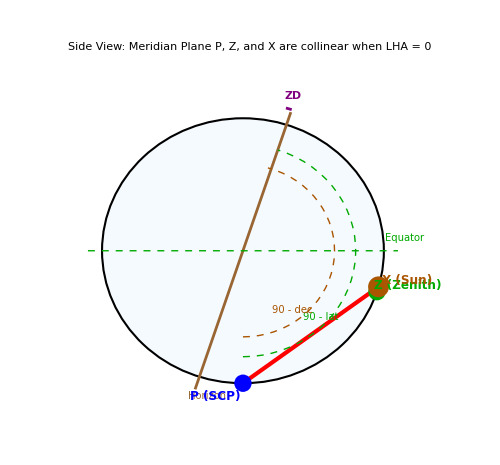

```mathematica
sideView
```

## Equation Summary Diagram

```mathematica
equationDiagram = Graphics[{
  {RGBColor[0.95, 0.95, 1], Rectangle[{0, 0}, {10, 8}]},
  Text[Style["Noon Sight: Triangle to Line", Bold, 18], {5, 7.5}],
  {EdgeForm[{Black, Thickness[0.002]}], White, Rectangle[{0.5, 5.5}, {9.5, 7}]},
  Text[Style["General Altitude Equation:", Bold, 12], {5, 6.6}],
  Text[Style["sin(h) = sin(lat)sin(dec) + cos(lat)cos(dec)cos(LHA)", 14], {5, 5.9}],
  {Thickness[0.003], Arrowheads[0.03], Arrow[{{5, 5.3}, {5, 4.7}}]},
  Text[Style["LHA = 0", Bold, 11, Red], {5.6, 5}],
  {EdgeForm[{Red, Thickness[0.003]}], RGBColor[1, 0.95, 0.95], Rectangle[{0.5, 3}, {9.5, 4.5}]},
  Text[Style["Simplified (cos(0) = 1):", Bold, 12], {5, 4.1}],
  Text[Style["sin(h) = sin(lat)sin(dec) + cos(lat)cos(dec) = cos(lat - dec)", 14], {5, 3.4}],
  {Thickness[0.003], Arrowheads[0.03], Arrow[{{5, 2.8}, {5, 2.2}}]},
  Text[Style["h = 90 - ZD", 11, Purple], {5.8, 2.5}],
  {EdgeForm[{Darker[Green], Thickness[0.004]}], RGBColor[0.9, 1, 0.9], Rectangle[{1.5, 0.5}, {8.5, 2}]},
  Text[Style["Noon Sight Formula:", Bold, 14, Darker[Green]], {5, 1.6}],
  Text[Style["Latitude = Declination +/- Zenith Distance", Bold, 16, Darker[Green]], {5, 1}]
},
ImageSize -> 550,
Background -> White
];
```

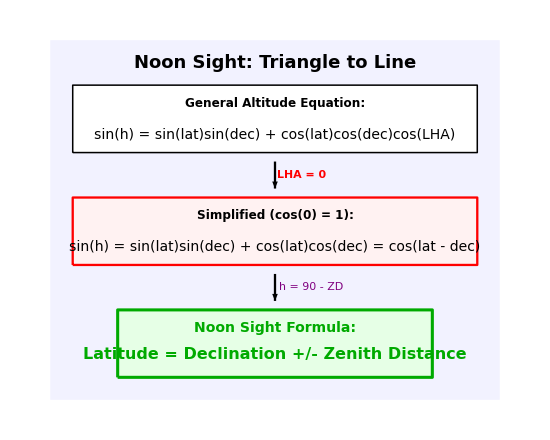

```mathematica
equationDiagram
```

## Export Commands

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["noon_sight_equation.png", equationDiagram, ImageResolution -> 150]
```

noon_sight_equation.png

```mathematica
Export["collinear_pzx_3d.png", collinearPZX, ImageResolution -> 150]
```

collinear_pzx_3d.png

```mathematica
Export["collinear_pzx_side.png", sideView, ImageResolution -> 150]
```

collinear_pzx_side.png